```mathematica
Off[Solve::svars]
SetDirectory[ NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_moments_deal/Mathematica_files

```mathematica
readMat[filename_]:=Module[{result},

result = StringJoin["boundary_matrices/heat_conduction_Hermite",filename];
result = Import[result,"Table",Precision->15]
]
```

## Tensor Definitions

```mathematica
(*Remove["Global`*"]*)
```

Mathematica build-in function like ‘Symmetrize[]’ and ‘TensorContract[]’ seem 
to work really slow or fail due to memory requirements on fully symmetric tensors 
with degree >10.
We define our own functions below based on a simply array data structure for fully symmetric tensors.

```mathematica
Clear[n,degree,idx,idx1,A,b,id3,IDX]
Unprotect[TensorDegree];

(*Every symmetric tensor can be identified with the help of a 2D array say a[N][3] where N is the total number of indepedent variables it has. So every row ie a[i] store the number of entries for x in a[i][1],for y in a[i][2] and for z in a[i][3]*)
IDXFull[n_]:=Flatten[Table[Table[{n-ii,ii-jj,jj},{jj,0,ii}],{ii,0,n}],1]

(*does the same thing as IDXFull but for trace free tensors*)
IDXtrfFull[n_]:=Flatten[Table[Table[{n-ii,ii-jj,jj},{jj,0,Min[ii,1]}],{ii,0,n}],1]

Do[
IDX[degree]=IDXFull[degree];
IDXtrf[degree]=IDXtrfFull[degree];
,{degree,0,40}]

(*given an array list, the following function counts the number of 1s, 2s and 3s*)
toIDX1[list_]:=Map[Count[list,#]&,{1,2,3}] (* Input cartesean indices, e.g. {1,1,2,1,3} *)

(*the Total of the list is the tensorial degree we are interested in. So list should be a 3X1 array and the following function will give us the n corresponding to which a[n] = list.*)
toIDX2[list_]:=Position[IDX[Total[list]],list]⟦1,1⟧ (* Input triple of #indices in {1,2,3} *)
(*same as above but for trace free tensors*)
toIDX3[list_]:=Position[IDXtrfFull[Total[list]],list]⟦1,1⟧ (* Input triple of #indices in {1,2,3} *)

(*Gives the tensor degree of a symmetric tensor.
CAUTION: the formulae is not valid for trace free tensors.*)
TensorDegree[A_]:=1/2 (-3+√(1+8 Length[A]))

id3={{1,0,0},{0,1,0},{0,0,1}};

DeltaValues[list_]:=Block[{a=list⟦1⟧,b=list⟦2⟧,c=list⟦3⟧},
If[OddQ[a]||OddQ[b]||OddQ[c],0,Multinomial[a/2,b/2,c/2]/Multinomial[a,b,c]]
];

(*applied deltavalues to all the components of an even degree tensor*)
DeltaTensor2[degree_?EvenQ]:=Map[DeltaValues,IDX[degree]];

(*What does this do?*)
SymTrace2[A_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
length=Length[IDX[degree-2]];
res=ConstantArray[0,length];
Do[
res⟦jj⟧=Expand[Sum[A⟦toIDX2[IDX[degree-2]⟦jj⟧+2 id3⟦ii⟧]⟧,{ii,1,dim}]];
,{jj,1,length}];

res
];

SymTraces[A_,n_]:=Module[{res=A},
Do[res=SymTrace2[res],{ii,1,n}];
res
];

(*if the format of the input is IDX, then the output is also in IDX,
Assumes 3 dimensions. And so *)
(* contraction of a symmetric tensor A with Subscript[b, i] *)
SymDot2[A_,b_?VectorQ]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
length=Length[IDX[degree-1]];
res=ConstantArray[0,length];
Do[
(*Lets take a particular term say Ai1i2..xbx. In the result only those components will appear in which x atleast appears once and that's why the addition of id3[[iis]]*)
res⟦jj⟧=Expand[Sum[A⟦toIDX2[IDX[degree-1]⟦jj⟧+id3⟦ii⟧]⟧b⟦ii⟧,{ii,1,dim}]];
,{jj,1,length}];

res
];

(*if the format of the input is IDX, then the output is also in IDX*)
(* full contraction of two symmetric tensors A, B with same degree *)
SymFullDot[A_,B_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
If[TensorDegree[B]≠degree,Return[0]];
length=Length[IDX[degree]];
res=0;
Do[
idx=IDX[degree]⟦jj⟧;
res+=Multinomial[idx⟦1⟧,idx⟦2⟧,idx⟦3⟧]A⟦jj⟧B⟦jj⟧;
,{jj,1,length}];

res
];

(* symmetric tensor product of a symmetric tensor A with Subscript[b, i] *)
SymProduct2[A_,b_?VectorQ]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
If[degree==0,Return[A⟦1⟧ b]];
length=Length[IDX[degree+1]];
res=ConstantArray[0,length];
Do[
res⟦jj⟧=
1/(degree+1)Sum[
If[(idx=IDX[degree+1]⟦jj⟧)⟦ii⟧>0,idx⟦ii⟧ A⟦toIDX2[idx-id3⟦ii⟧]⟧b⟦ii⟧,0],{ii,1,dim}];
,{jj,1,length}];

res
];

(* symmetric tensor product of a symmetric tensor A with Subscript[δ, ij] *)
SymProductDelta2[A_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
length=Length[IDX[degree+2]];
res=ConstantArray[0,length];
Do[
res⟦jj⟧=1/((degree+2)(degree+1))Sum[
If[(idx=IDX[degree+2]⟦jj⟧)⟦ii⟧≥2,idx⟦ii⟧(idx⟦ii⟧-1)A⟦toIDX2[idx-2id3⟦ii⟧]⟧,0],{ii,1,dim}];
,{jj,1,length}];

res
];

(*converts a symmetric tensor into a trace free tensor*)
(* returns the tracefree part of a symmetric tensor, but with all components *)
SymTracefree[A_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res,trace,res1},
length=Length[IDX[degree]];
res=trace=A;
Do[
res1=trace=SymTrace2[trace];
Do[res1=SymProductDelta2[res1],{ll,1,kk}];
res+=(((-1)^kk degree!)/((degree-2kk)!2^kk kk!)∏_(jj=degree-kk)^(degree-1) 1/(2jj+1))res1;
,{kk,1,degree/2}];

res
];
```

```mathematica
trfEvaluate[A_,list_]:=Module[{a,b,c,m,dim=3,degree=(Length[A]-1)/2,length,res},
{a,b,c}=list;
m=Floor[c/2];
If[c≤1,
res=A⟦toIDX3[list]⟧,
res=(-1)^m Sum[Binomial[m,i]A⟦toIDX3[list+2i id3⟦1⟧+2(m-i) id3⟦2⟧-2m id3⟦3⟧]⟧,{i,0,m}]
];
res
];

(*say we have a trace free tensor, whose independent components are given then the following function will introduce those components in the list which have been negelected due to the trace free nature of the tensor. For eg. it will introduce -Rxx-Ryy for a second order tensor*)
trf2sym[A_]:=Map[Apply[trfEvaluate[A,{#1,#2,#3}]&,#]&,IDX[(Length[A]-1)/2]]

(*Pick the 2D variables from a list containing all the indices.The list will be obtained from the IDXtrf routine. freeindex is the total number of free indices in the tensor*)
Pick2D[freeindex_]:=Pick[IDXtrf[freeindex],Flatten[Join[{1},Table[{1,0},{k,1,freeindex}]]],1];
```

```mathematica
SymTensorForm[A_]:=Block[{degree=TensorDegree[A],length},
length=Length[IDX[degree]];
Table[Apply[{$[#1,#2,#3],A⟦ii⟧}&,IDX[degree]⟦ii⟧],{ii,1,length}]//TableForm
];
```

```mathematica
SymProductDelta2[SymProductDelta2[SymProductDelta2[Map[Apply[A[#1,#2,#3]&,#]&,IDX[1]]]]]
```

{A[1,0,0],1/7 A[0,1,0],1/7 A[0,0,1],1/7 A[1,0,0],0,1/7 A[1,0,0],3/35 A[0,1,0],1/35 A[0,0,1],1/35 A[0,1,0],3/35 A[0,0,1],3/35 A[1,0,0],0,1/35 A[1,0,0],0,3/35 A[1,0,0],1/7 A[0,1,0],1/35 A[0,0,1],1/35 A[0,1,0],1/35 A[0,0,1],1/35 A[0,1,0],1/7 A[0,0,1],1/7 A[1,0,0],0,1/35 A[1,0,0],0,1/35 A[1,0,0],0,1/7 A[1,0,0],A[0,1,0],1/7 A[0,0,1],1/7 A[0,1,0],3/35 A[0,0,1],3/35 A[0,1,0],1/7 A[0,0,1],1/7 A[0,1,0],A[0,0,1]}

```mathematica
Expand[SymTracefree[Map[Apply[A[#1,#2,#3]&,#]&,IDX[2]]]]
```

{-1/3 A[0,0,2]-1/3 A[0,2,0]+2/3 A[2,0,0],A[1,1,0],A[1,0,1],-1/3 A[0,0,2]+2/3 A[0,2,0]-1/3 A[2,0,0],A[0,1,1],2/3 A[0,0,2]-1/3 A[0,2,0]-1/3 A[2,0,0]}

```mathematica
Expand[SymTracefree[Map[Apply[#1+2.#2-3#3&,#]&,IDX[4]]]]
```

{-1.14286,1.14286,2.57143,3.42857,1.42857,-2.28571,3.14286,2.85714,-4.28571,-5.42857,-2.28571,4.28571,-1.14286,-5.71429,3.42857}

```mathematica
Expand[SymFullDot[SymTracefree[trf2sym[{Rxx,Rxy,0,Ryy,0}]],SymTracefree[trf2sym[{Sxx,Sxy,0,Syy,0}]]]]
```

2 Rxx Sxx+Ryy Sxx+2 Rxy Sxy+Rxx Syy+2 Ryy Syy

```mathematica
Normal[CoefficientArrays[Normal[CoefficientArrays[Expand[SymFullDot[SymTracefree[trf2sym[{Rxx,Rxy,0,Ryy,0}]],SymTracefree[trf2sym[{Sxx,Sxy,0,Syy,0}]]]],{Rxx,Rxy,Ryy}]]⟦2⟧,{Sxx,Sxy,Syy}]⟦2⟧]
```

{{2,0,1},{0,2,0},{1,0,2}}

```mathematica
Normal[CoefficientArrays[Normal[CoefficientArrays[Expand[SymFullDot[SymTracefree[trf2sym[{mxxx,mxxy,0,mxyy,0,myyy,0}]],SymTracefree[trf2sym[{nxxx,nxxy,0,nxyy,0,nyyy,0}]]]],{mxxx,mxxy,mxyy,myyy}]]⟦2⟧,{nxxx,nxxy,nxyy,nyyy}]⟦2⟧]
```

{{4,0,3,0},{0,6,0,3},{3,0,6,0},{0,3,0,4}}

## Get Matrices

### Develop Macroscopic

```mathematica
Developθ[sol_,var_]:=(√2)/3 Total[sol⟦{4,6,7}⟧];
Developqy[sol_,var_]:=1/(√2)(√3 sol⟦Flatten[Position[var,{0,3,0}]]⟧+sol⟦Flatten[Position[var,{2,1,0}]]⟧+sol⟦Flatten[Position[var,{0,1,2}]]⟧);

Developσxx[sol_,var_]:=(√2)/3(2sol⟦4⟧-sol⟦6⟧-sol⟦7⟧);
```

### Core routines

```mathematica
HSpcInt[n_,m_]:=Which[m==n,1/2,OddQ[m-n],1/(√(2 π))(√(n!m!))/(n!)(∑_(i=1)^n (2^(1/2 (1-2 i+m+n)) π)/(Gamma[(i-m)/2] Gamma[2-i+m] Gamma[1/2 (1+i-n)])+((m-n-2)!!(-1)^((m-n-1)/2))/((m-n)!)),EvenQ[m-n],0];

IDXFull2D[M_]:=Select[IDXFull[M],(EvenQ[#⟦3⟧])&];
IDXFull2DOdd[M_]:=Select[Select[IDXFull[M],(EvenQ[#⟦3⟧])&],(OddQ[#⟦1⟧])&];

DevelopBC[bc_,var_]:=Module[{rhoW,bCond,rhoWSol},

bCond = (bc.var-bc⟦All,1⟧rhoW)/.{w[1,0,0]->0};
rhoWSol = Solve[bCond⟦1⟧==0,rhoW]⟦1⟧;
bCond = bCond/.rhoWSol;
bCond⟦1⟧=w[1,0,0]/2;
bCond = CoefficientArrays[Table[ii==0,{ii,bCond}],var]⟦2⟧;

Simplify[bCond]

]

(*truncate matrices for better convergence*)
TruncateMat[Ax_,B_,P_,M_]:=Module[{var,varTrun,loc},

var = Flatten[Table[IDXFull2D[ii],{ii,0,M}],1];
varTrun = Flatten[{Flatten[Table[IDXFull2D[ii],{ii,0,M-1}],1],IDXFull2DOdd[M]},1];

loc = Flatten[Position[var,Alternatives@@varTrun]];

{Ax⟦loc,loc⟧,B⟦All,loc⟧,P⟦loc,loc⟧,varTrun}
]

GetProduction[var_]:=Module[{P,W200,W020,W002},

W200 = Flatten[Position[var,w[2,0,0]]];
W020 = Flatten[Position[var,w[0,2,0]]];
W002 = Flatten[Position[var,w[0,0,2]]];

P = DiagonalMatrix[Table[-1,{ii,1,Length[var]}]];

P⟦W200,{W200⟦1⟧,W020⟦1⟧,W002⟦1⟧}⟧ = {-2/3,1/3,1/3};
P⟦W020,{W200⟦1⟧,W020⟦1⟧,W002⟦1⟧}⟧ = {1/3,-2/3,1/3};
P⟦W002,{W200⟦1⟧,W020⟦1⟧,W002⟦1⟧}⟧ = {1/3,1/3,-2/3};

(*for mass momentum and energy*)
P⟦{1,2,3},{1,2,3}⟧=0;

P

]

CheckSPSD[Mat_]:=Module[{result,ev},
ev = Eigenvalues[Mat];
ev = Select[ev,(#<0)&];
If[Length[ev]==0,Print[Style["PSD",FontColor->Green]],Print[Style["NSD",FontColor->Green]]];

If[Norm[Mat-Transpose[Mat]]==0,Print[Style["S",FontColor->Green]],Print[Style["NS",FontColor->Green]]];

]

StabilizeBoundary[Ax_,B_,var_,M_]:=Module[{varOdd,varEven,Aoe,Boe,Btemp,MatOnsager},

varOdd = Flatten[Position[var,Alternatives@@Select[var,(OddQ[#⟦1⟧])&]]];
varEven = Flatten[Position[var,Alternatives@@Select[var,(EvenQ[#⟦1⟧])&]]];

Aoe = Ax⟦varOdd,varEven⟧;

(*2 comes from the left of the boundary conditions i.e. the factor infront of the odd variables. *)
Boe = -2*B⟦All,varEven⟧;

(*Mat Onsager*)
MatOnsager = Boe⟦All,1;;Length[varOdd]⟧.Inverse[Aoe⟦All,1;;Length[varOdd]⟧];

(*stabilize Boe*)
Boe = MatOnsager.Aoe;

Btemp = B;
Btemp⟦All,varOdd⟧ = IdentityMatrix[Length[varOdd]];
Btemp⟦All,varEven⟧ = -Boe;

Btemp
]
```

#### Flux matrices

```mathematica
GetMatrixHermite[M_,flag_]:=Module[{varIdxComplete,Ax,ia,ja,va,numVar,indexMinus,indexPlus,data,EvenCat3,OddVar,EvenVar,intEven,idxOdd,var,bc,filenameAx,filenameB,P,filenameP,filenameSigma,filenameOddID},

(*all the idx. Already converted to 2D*)
varIdxComplete = Flatten[Table[IDXFull2D[ii],{ii,0,M}],1];

var = Map[Apply[w,#]&,varIdxComplete];
OddVar = Select[varIdxComplete,(OddQ[#⟦1⟧])&];
numVar = Length[varIdxComplete];

ia = ConstantArray[0,{numVar-Length[IDXFull2D[M]]}];
ja = ConstantArray[0,{numVar-Length[IDXFull2D[M]]}];
va = ConstantArray[0,{numVar-Length[IDXFull2D[M]]}];

Do[
ia⟦ii⟧ = ii;

indexPlus = {varIdxComplete⟦ii⟧⟦1⟧+1,varIdxComplete⟦ii⟧⟦2⟧,varIdxComplete⟦ii⟧⟦3⟧};

ja⟦ii⟧ = Flatten[Position[varIdxComplete,indexPlus]]⟦1⟧;
va⟦ii⟧ = Sqrt[varIdxComplete⟦ii⟧⟦1⟧+1];

,{ii,1,numVar-Length[IDXFull2D[M]]}];

(*account for the symmetry of the matrix*)
data = Flatten[{Table[{ia⟦ii⟧,ja⟦ii⟧}->va⟦ii⟧,{ii,1,Length[ia]}],Table[{ja⟦ii⟧,ia⟦ii⟧}->va⟦ii⟧,{ii,1,Length[ia]}]},1];

Ax = SparseArray[data,{numVar,numVar}];

intEven = ConstantArray[0,{Length[OddVar],1}];

Do[
EvenVar = Select[varIdxComplete,(#⟦2⟧==OddVar⟦ii⟧⟦2⟧&&#⟦3⟧==OddVar⟦ii⟧⟦3⟧&&EvenQ[#⟦1⟧])&];

intEven⟦ii⟧=Table[HSpcInt[OddVar⟦ii⟧⟦1⟧,jj⟦1⟧],{jj,EvenVar}].Map[Apply[w,#]&,EvenVar];
,{ii,1,Length[OddVar]}];

intEven = Map[Apply[w,#]&,OddVar]/2-intEven;
bc = CoefficientArrays[Table[ii==0,{ii,intEven}],var]⟦2⟧;
bc = DevelopBC[bc,var];

P= GetProduction[var];

If[flag==1,
{Ax,bc,P,var}=TruncateMat[Ax,bc,P,M];,
bc = StabilizeBoundary[Ax,bc,var,M];
var=varIdxComplete;
];

{Ax,P,bc,var}

]
```

## Solving Routines

### Order the EV

```mathematica
OrderEV[v_,λ_]:=Module[{ascend,λtemp,vtemp,jj,pair,numEnt},

ascend = Ordering[λ];

λtemp = λ⟦ascend⟧;
vtemp= v⟦ascend⟧;
numEnt = Length[λtemp];

If[OddQ[numEnt],Print["Bad system"]];

pair = {};

(*we assume that the pariwise eigenvalues have eigenvectors such that the absolute of the entries is the same.*)

Do[
Do[If[Tr@Unitize[Chop[Abs[vtemp⟦ii⟧]-Abs[vtemp⟦jj⟧]]]==0,pair=Insert[pair,{ii,jj},-1];],{jj,numEnt/2+1,numEnt}],{ii,1,numEnt/2}];

pair = Flatten[pair];

If[Length[pair]≠numEnt,Print["Eigenvalue ordering not right"];Abort[];];

{vtemp⟦pair⟧,λtemp⟦pair⟧}
]
```

### returns the solution heat conduction

```mathematica
Clear[nvar,kn,thetaw,A0,P0,λ0,λ,λPlus,v,vv,B0,alpha,coef,Kn,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC,α,BC]

(*flag = 0 for grad, flag == 1 for truncated systems, problemtype == 0 for poisson hc and 0 for heat conduction*)
GetSolutionHeat[M_,θW_,kn_,alpha_,systemtype_,problemtype_]:=Block[{λ0,λ,λPlus,v,vv,coef,Kn,vW,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC,bc,nvar,α,posλ,thetaW,BCmatrix,BCrhs,toSolve},

If[problemType==0,Print[Style["Poisson Heat Conduction",FontColor->Pink]],Print[Style["Heat Conduction",FontColor->Pink]]];

{A0,P0,BC,variables}=GetMatrixHermite[M,systemtype];
nvar = Length[A0];


{λ0,vv}=Chop[Eigensystem[{P0,N[1.0A0]}],10^-7];
λ=Re[Select[λ0,(0<Abs[#]<∞)&]];

posλ=Delete[Range[1,Length[λ0]],Join[Position[λ0,0],Position[λ0,∞],Position[λ0,ComplexInfinity],Position[λ0,∞ ⅈ]]];

v=vv⟦Flatten[posλ]⟧;

{v,λ} = OrderEV[v,λ];

λ=Flatten[Table[{Rationalize[λ⟦ii⟧,0],-Rationalize[λ⟦ii⟧,0]},{ii,1,Length[λ],2}]];

λPlus=Select[λ,(#>0)&];

B0=Table[0,{i,1,nvar}];
If[problemtype==0, B0⟦{4,6,7}⟧=(√2)/3{1,1,1}];

If[problemtype==1,coef[0,Flatten[Position[variables,{3,0,0}]]⟦1⟧]=√3 k[0];coef[0,Flatten[Position[variables,{1,2,0}]]⟦1⟧]=k[0];coef[0,Flatten[Position[variables,{1,0,2}]]⟦1⟧]=k[0]];

Ansatz[x_]=Table[Sum[coef[jj,ii] x^jj,{jj,0,4}],{ii,1,nvar}];
Coefs=Cases[Flatten[Table[Table[coef[jj,ii],{jj,0,4}],{ii,1,nvar}]],coef[_,_]];

Ansatz[x_]=Ansatz[x]/.Solve[Thread[Flatten[CoefficientList[A0.Ansatz'[x]-1/Kn P0.Ansatz[x]-α B0 x^2,x]]==0],Coefs]⟦1⟧/.{coef[_,_]->0};

SymmetryConditions=Table[0,{ii,1,Length[λ],2}];

If[problemtype==0,
Do[jj=1;While[v⟦ii,jj⟧==0,jj++];SymmetryConditions⟦(ii+1)/2⟧=(k[ii]->(Sign[v⟦ii+1,jj⟧/v⟦ii,jj⟧])k[ii+1]),{ii,1,Length[λ],2}],Do[jj=1;While[v⟦ii,jj⟧==0,jj++];SymmetryConditions⟦(ii+1)/2⟧=(k[ii]->-(Sign[v⟦ii+1,jj⟧/v⟦ii,jj⟧])k[ii+1]),{ii,1,Length[λ],2}]];

(*The following additon of the eigenmodes is the homogeneous solution to the problem. But why the term C0B0?*)
solution=ExpToTrig[C0 B0+Ansatz[x]+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn],{ii,1,Length[λ]}]/.SymmetryConditions/.Table[k[ii]->k[ii/2],{ii,1,Length[λ]}]];

res=Thread[Table[α[i],{i,0,nvar-1}]->solution/.Table[k[ii]->k[ii]Exp[-λPlus⟦ii⟧(1/2)/Kn],{ii,1,Length[λPlus]}]];


bc=BC.Map[α[#]&,Range[0,nvar-1]]-1/(√2)thetaW( BC⟦All,4⟧+BC⟦All,6⟧+BC⟦All,7⟧);

bcEqn=bc/.res/.{Kn->kn,thetaW->θW,α->alpha,x->1/2};

If[problemtype==0,toSolve = Flatten[Join[{C0},Table[k[ii],{ii,1,Length[λ]/2}]]];,toSolve = Flatten[Join[{k[0]},Table[k[ii],{ii,1,Length[λ]/2}]]];];

solBC=Solve[Thread[bcEqn==0],toSolve]⟦1⟧;


Table[α[i],{i,0,nvar-1}]/.res/.solBC/.{Kn->kn}/.α->alpha

]
```

Part::partd: Part specification 0.0000102143⟦{4,6,7}⟧ is longer than depth of object.

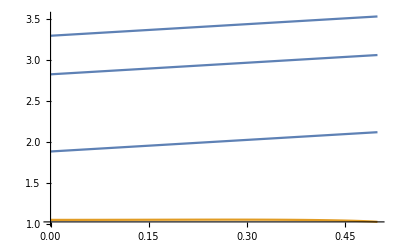

```mathematica
Plot[{(√2)/3(Total[solPoissonGradKn0p1[3][x]⟦1⟧⟦{4,6,7}⟧]),θExactKn0p1[x]},{x,0,0.5}]
```

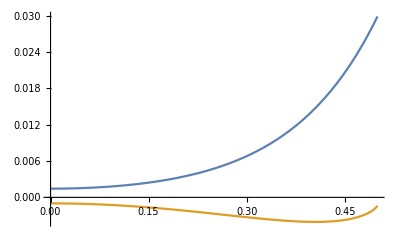

```mathematica
Plot[{(√2)/3(2trialu[x]⟦4⟧-trialu[x]⟦6⟧-trialu[x]⟦7⟧),σExactKn0p1[x]},{x,0,0.5}]
```

### returns the solution momentum problem

```mathematica
Clear[nvar,kn,thetaw,A0,P0,λ0,λ,λPlus,v,vv,B0,alpha,coef,Kn,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC,α,BC,variables]

(*flag = 0 for grad, flag == 1 for truncated systems, problemtype == 0 for poisson shear and 0 for shear flow*)

GetSolutionMomentum[M_,vW_,kn_,alpha_,systemtype_,problemtype_]:=Block[{λ0,λ,λPlus,v,vv,coef,Kn,k,velW,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC,bc,nvar,α,posλ,thetaW,BCmatrix,BCrhs,toSolve},

Print[problemtype];

If[problemtype==0,Print[Style["Poisson Shear",FontColor->Pink]];,Print[Style["Shear",FontColor->Pink]];];

{A0,P0,BC,variables}=GetMatrixHermite[M,systemtype];
nvar = Length[A0];


{λ0,vv}=Chop[Eigensystem[{P0,N[1.0A0]}],10^-7];
λ=Re[Select[λ0,(0<Abs[#]<∞)&]];

posλ=Delete[Range[1,Length[λ0]],Join[Position[λ0,0],Position[λ0,∞],Position[λ0,ComplexInfinity],Position[λ0,∞ ⅈ]]];

v=vv⟦Flatten[posλ]⟧;

{v,λ} = OrderEV[v,λ];

λ=Flatten[Table[{Rationalize[λ⟦ii⟧,0],-Rationalize[λ⟦ii⟧,0]},{ii,1,Length[λ],2}]];

λPlus=Select[λ,(#>0)&];

B0=Table[0,{i,1,nvar}];
If[problemtype==0, B0⟦3⟧=1];

If[problemtype==1,coef[0,Flatten[Position[variables,{1,1,0}]]⟦1⟧]=k[0];];

Ansatz[x_]=Table[Sum[coef[jj,ii] x^jj,{jj,0,4}],{ii,1,nvar}];
Coefs=Cases[Flatten[Table[Table[coef[jj,ii],{jj,0,4}],{ii,1,nvar}]],coef[_,_]];

Ansatz[x_]=Ansatz[x]/.Solve[Thread[Flatten[CoefficientList[A0.Ansatz'[x]-1/Kn P0.Ansatz[x]-α B0 ,x]]==0],Coefs]⟦1⟧/.{coef[_,_]->0};

SymmetryConditions=Table[0,{ii,1,Length[λ],2}];

If[problemtype==0,
Do[jj=1;While[v⟦ii,jj⟧==0,jj++];SymmetryConditions⟦(ii+1)/2⟧=(k[ii]->(Sign[v⟦ii+1,jj⟧/v⟦ii,jj⟧])k[ii+1]),{ii,1,Length[λ],2}],Do[jj=1;While[v⟦ii,jj⟧==0,jj++];SymmetryConditions⟦(ii+1)/2⟧=(k[ii]->-(Sign[v⟦ii+1,jj⟧/v⟦ii,jj⟧])k[ii+1]),{ii,1,Length[λ],2}]];

(*The following additon of the eigenmodes is the homogeneous solution to the problem. But why the term C0B0?*)
solution=ExpToTrig[C0 B0+Ansatz[x]+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn],{ii,1,Length[λ]}]/.SymmetryConditions/.Table[k[ii]->k[ii/2],{ii,1,Length[λ]}]];

res=Thread[Table[α[i],{i,0,nvar-1}]->solution/.Table[k[ii]->k[ii]Exp[-λPlus⟦ii⟧(1/2)/Kn],{ii,1,Length[λPlus]}]];


bc=BC.Map[α[#]&,Range[0,nvar-1]]-velW BC⟦All,3⟧;

bcEqn=bc/.res/.{Kn->kn,velW->vW/2,α->alpha,x->1/2};

If[problemtype==0,toSolve = Flatten[Join[{C0},Table[k[ii],{ii,1,Length[λ]/2}]]];,toSolve = Flatten[Join[{k[0]},Table[k[ii],{ii,1,Length[λ]/2}]]];];

solBC=Solve[Thread[bcEqn==0],toSolve]⟦1⟧;

Table[α[i],{i,0,nvar-1}]/.res/.solBC/.{Kn->kn}/.α->alpha

]
```

# Reference Solution

### Poisson Heat

```mathematica
exactKn0p1 = Import["refs/Archive/BGKPoiseuilleHeat/Result_BGKreduced_tau0p1_nst600_Nc300_cMax5p0.dat"];

exactKn0p3 = Import["refs/Archive/BGKPoiseuilleHeat/Result_BGKreduced_tau0p3_nst600_Nc300_cMax5p0.dat"];

exactKn0p5 = Import["refs/Archive/BGKPoiseuilleHeat/Result_BGKreduced_tau0p5_nst600_Nc300_cMax5p0.dat"];

(*fix for the wall temperature. The problem is linear in nature*)
exactKn0p1⟦All,4⟧+=1;
exactKn0p3⟦All,4⟧+=1;
exactKn0p5⟦All,4⟧+=1;

θExactKn0p1=Interpolation[exactKn0p1⟦All,{1,4}⟧];
σExactKn0p1 = Interpolation[exactKn0p1⟦All,{1,6}⟧];
qExactKn0p1 = Interpolation[exactKn0p1⟦All,{1,7}⟧];

θExactKn0p3=Interpolation[exactKn0p3⟦All,{1,4}⟧];
σExactKn0p3 = Interpolation[exactKn0p3⟦All,{1,6}⟧];
qExactKn0p3 = Interpolation[exactKn0p3⟦All,{1,7}⟧];

θExactKn0p5=Interpolation[exactKn0p5⟦All,{1,4}⟧];
σExactKn0p5 = Interpolation[exactKn0p5⟦All,{1,6}⟧];
qExactKn0p5 = Interpolation[exactKn0p5⟦All,{1,7}⟧];
```

```mathematica
θExactKn0p3[x]
```

InterpolatingFunction[{{-0.5, 0.5}}, <>][x]

### Heat Conduction

```mathematica
exactHCKn0p1 = Import["refs/Archive/BGKSimpleHeat/Result_BGKreduced_tau0p1_nst600_Nc300_cMax5p0.dat"];

exactHCKn0p3 = Import["refs/Archive/BGKSimpleHeat/Result_BGKreduced_tau0p3_nst600_Nc300_cMax5p0.dat"];

exactHCKn0p5 = Import["refs/Archive/BGKSimpleHeat/Result_BGKreduced_tau0p5_nst600_Nc300_cMax5p0.dat"];

(*fix for the wall temperature*)
(*exactHCKn0p1⟦All,4⟧+=1;
exactHCKn0p3⟦All,4⟧+=1;
exactHCKn0p5⟦All,4⟧+=1;*)

θExactHCKn0p1=Interpolation[exactHCKn0p1⟦All,{1,4}⟧];
σExactHCKn0p1 = Interpolation[exactHCKn0p1⟦All,{1,6}⟧];
qExacHCtKn0p1 = Interpolation[exactHCKn0p1⟦All,{1,7}⟧];

θExactHCKn0p3=Interpolation[exactHCKn0p3⟦All,{1,4}⟧];
σExactHCKn0p3 = Interpolation[exactHCKn0p3⟦All,{1,6}⟧];
qExactHCKn0p3 = Interpolation[exactHCKn0p3⟦All,{1,7}⟧];

θExactHCKn0p5=Interpolation[exactHCKn0p5⟦All,{1,4}⟧];
σExactHCKn0p5 = Interpolation[exactHCKn0p5⟦All,{1,6}⟧];
qExactHCKn0p5 = Interpolation[exactHCKn0p5⟦All,{1,7}⟧];
```

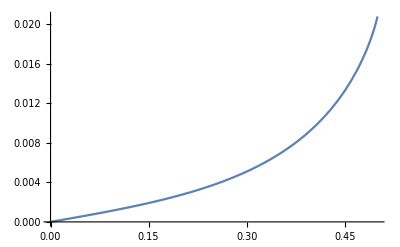

```mathematica
Plot[σExactHCKn0p1[x],{x,0,0.5}]
```

### Poisson Shear

```mathematica
exactPoissonShearKn0p1 = Import["refs/Archive/BGKPoiseuilleFlow/Result_BGKreduced_tau0p1_nst600_Nc300_cMax5p0.dat"];

exactPoissonShearKn0p3 = Import["refs/Archive/BGKPoiseuilleFlow/Result_BGKreduced_tau0p3_nst600_Nc300_cMax5p0.dat"];

exactPoissonShearKn0p5 = Import["refs/Archive/BGKPoiseuilleFlow/Result_BGKreduced_tau0p5_nst600_Nc300_cMax5p0.dat"];

(*fix for the wall velocity*)
exactPoissonShearKn0p1⟦All,2⟧+=0.5;
exactPoissonShearKn0p3⟦All,2⟧+=0.5;
exactPoissonShearKn0p5⟦All,2⟧+=0.5;

vyExactPoissonShearKn0p1=Interpolation[exactPoissonShearKn0p1⟦All,{1,2}⟧];
qyExactPoissonShearKn0p1=Interpolation[exactPoissonShearKn0p1⟦All,{1,4}⟧];
```

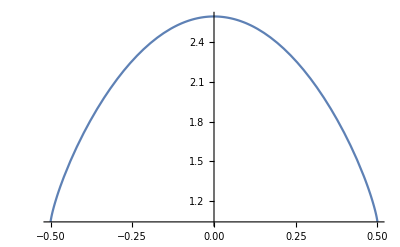

```mathematica
Plot[vyExactPoissonShearKn0p1[x],{x,-0.5,0.5}]
```

```mathematica
vyExactPoissonShearKn0p1[0.5]
```

0.543269

### Shear

```mathematica
exactShearKn0p1 = Import["refs/Archive/BGKCouetteFlow/Result_BGKreduced_tau0p1_nst600_Nc300_cMax5p0.dat"];

exactShearKn0p3 = Import["refs/Archive/BGKCouetteFlow/Result_BGKreduced_tau0p3_nst600_Nc300_cMax5p0.dat"];

exactShearKn0p5 = Import["refs/Archive/BGKCouetteFlow/Result_BGKreduced_tau0p5_nst600_Nc300_cMax5p0.dat"];


vyExactShearKn0p1=Interpolation[exactShearKn0p1⟦All,{1,2}⟧];
qyExactShearKn0p1=Interpolation[exactShearKn0p1⟦All,{1,4}⟧];
```

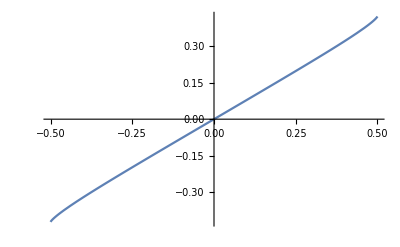

```mathematica
Plot[vyExactShearKn0p1[x],{x,-0.5,0.5}]
```

```mathematica
vyExactPoissonShearKn0p1[0.5]
```

0.543269

# Poisson Heat Conduction

```mathematica
Clear[solPoissonGradKn0p1]
```

### Error Computation

```mathematica
ComputeL2Diff[sol1_,sol2_]:=√2 Sqrt[NIntegrate[(sol1-sol2)^2,{x,0,0.5}]];

ComputeEntropyDiff[sol1_,sol2_,var1_,var2_]:=Module[{commonVar,result,temp},

(*we assume that sol1 is the reference solution and sol2 if not.*)
If[Length[var1]≤Length[var2],Print[Style["Incorrect inputs",FontColor->Red]];Abort[];];

(*the variables which are common between the two*)
commonVar = Position[var1,Alternatives@@var2];

temp = Flatten[commonVar];

(*error from the first few moments*)
result = √2 Total[Table[Sqrt[NIntegrate[(sol1⟦temp⟦ii⟧⟧-sol2⟦ii⟧)^2,{x,0,0.5}]],{ii,1,Length[var2]}]];

(*add the remaining moments*)
result = result+√2 Total[Table[Sqrt[NIntegrate[sol1⟦ii⟧^2,{x,0,0.5}]],{ii,Delete[Range[1,Length[var1]],commonVar]}]];

result
];
```

### Kn = 0.1

```mathematica
θW = 1;
Kn = 0.1;
alpha = 1;
problemType = 0;
```

```mathematica
systemType = 0;
solPoissonGradKn0p1[15][x]=GetSolutionHeat[15,θW,Kn,alpha,systemType,problemType];
varGrad[15]=variables;
```

Poisson Heat Conduction

```mathematica
(*GetSolutionHeat[M_,θW_,kn_,alpha_,flag_,problemtype_]*)

systemType = 0;
Do[Print[Style["Ntensors: ",FontColor->Pink]];Print[ii];
solPoissonGradKn0p1[ii][x]=GetSolutionHeat[ii,θW,Kn,alpha,systemType,problemType];
varGrad[ii]=variables;,{ii,3,10}];
```

Ntensors:

3

Poisson Heat Conduction

Ntensors:

4

Poisson Heat Conduction

Ntensors:

5

Poisson Heat Conduction

Ntensors:

6

Poisson Heat Conduction

Ntensors:

7

Poisson Heat Conduction

Ntensors:

8

Poisson Heat Conduction

Ntensors:

9

Poisson Heat Conduction

Ntensors:

10

Poisson Heat Conduction

```mathematica
systemType=1;
solPoissonTrunGradKn0p1[15][x]=GetSolutionHeat[15,θW,Kn,alpha,systemType,problemType];
varTrun[15]=variables;
```

Poisson Heat Conduction

```mathematica
systemType=1;
Do[Print[Style["Ntensors: ",FontColor->Pink]];Print[ii];
solPoissonTrunGradKn0p1[ii][x]=GetSolutionHeat[ii,θW,Kn,alpha,systemType,problemType];
varTrun[ii]=variables;,{ii,3,10}];
```

Ntensors:

3

Poisson Heat Conduction

Ntensors:

4

Poisson Heat Conduction

Ntensors:

5

Poisson Heat Conduction

Ntensors:

6

Poisson Heat Conduction

Ntensors:

7

Poisson Heat Conduction

Ntensors:

8

Poisson Heat Conduction

Ntensors:

9

Poisson Heat Conduction

Ntensors:

10

Poisson Heat Conduction

### Error Computation

#### Error Macroscopic

```mathematica
errorθKn0p1Grad = Table[ComputeL2Diff[(√2)/3 Total[solPoissonGradKn0p1[ii][x]⟦{4,6,7}⟧],θExactKn0p1[x]],{ii,3,10}];
errorθKn0p1TrunGrad = Table[ComputeL2Diff[(√2)/3 Total[solPoissonTrunGradKn0p1[ii][x]⟦{4,6,7}⟧],θExactKn0p1[x]],{ii,3,10}];
```

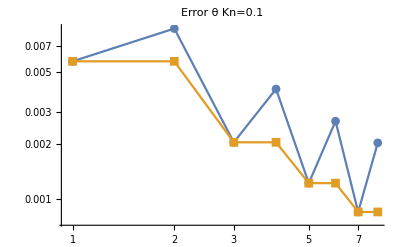

```mathematica
ListLogLogPlot[{errorθKn0p1Grad,errorθKn0p1TrunGrad},Joined->True,PlotLabel->"Error θ Kn=0.1",PlotMarkers->Automatic]
```

```mathematica
errorσKn0p1Grad = Table[ComputeL2Diff[(√2)/3(2solPoissonGradKn0p1[ii][x]⟦4⟧-solPoissonGradKn0p1[ii][x]⟦6⟧-solPoissonGradKn0p1[ii][x]⟦7⟧),σExactKn0p1[x]],{ii,3,10}];

errorσKn0p1TrunGrad = Table[ComputeL2Diff[(√2)/3(2solPoissonTrunGradKn0p1[ii][x]⟦4⟧-solPoissonTrunGradKn0p1[ii][x]⟦6⟧-solPoissonTrunGradKn0p1[ii][x]⟦7⟧),σExactKn0p1[x]],{ii,3,10}];
```

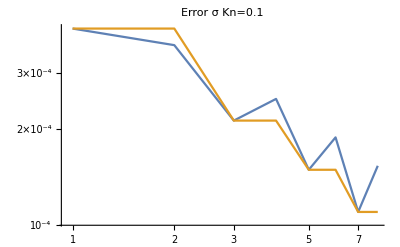

```mathematica
ListLogLogPlot[{errorσKn0p1Grad,errorσKn0p1TrunGrad},Joined->True,PlotLabel->"Error σ Kn=0.1"]
```

#### Error Entropy

```mathematica
errorEntropyTrunGradKn0p1=Table[ComputeEntropyDiff[solPoissonTrunGradKn0p1[15][x],solPoissonTrunGradKn0p1[ii][x],varTrun[15],varTrun[ii]],{ii,3,10}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
errorEntropyGradKn0p1=Table[ComputeEntropyDiff[solPoissonTrunGradKn0p1[15][x],solPoissonGradKn0p1[ii][x],varTrun[15],varGrad[ii]],{ii,3,10}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

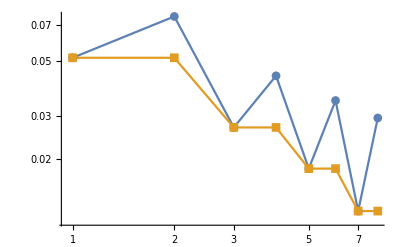

```mathematica
ListLogLogPlot[{errorEntropyGradKn0p1,errorEntropyTrunGradKn0p1},Joined->True,PlotMarkers->Automatic]
```

# Heat Conduction

```mathematica
Clear[solHCGradKn0p1]
```

### Kn = 0.1

```mathematica
θW = -1;
Kn = 0.1;
alpha = 0;
problemType = 1;
```

```mathematica
systemType = 0;
solHCGradKn0p1[15][x]=GetSolutionHeat[15,θW,Kn,alpha,systemType,problemType];
varGrad[15]=variables;
```

Heat Conduction

```mathematica
(*GetSolutionHeat[M_,θW_,kn_,alpha_,flag_,problemtype_]*)

systemType = 0;
Do[Print[Style["Ntensors: ",FontColor->Pink]];Print[ii];
solHCGradKn0p1[ii][x]=GetSolutionHeat[ii,θW,Kn,alpha,systemType,problemType];
varGrad[ii]=variables;,{ii,3,10}];
```

Ntensors:

3

Heat Conduction

Ntensors:

4

Heat Conduction

Ntensors:

5

Heat Conduction

Ntensors:

6

Heat Conduction

Ntensors:

7

Heat Conduction

Ntensors:

8

Heat Conduction

Ntensors:

9

Heat Conduction

Ntensors:

10

Heat Conduction

```mathematica
systemType = 1;
solHCTrunGradKn0p1[15][x]=GetSolutionHeat[15,θW,Kn,alpha,systemType,problemType];
varTrun[15]=variables;
```

Heat Conduction

```mathematica
systemType=1;
Do[Print[Style["Ntensors: ",FontColor->Pink]];Print[ii];
solHCTrunGradKn0p1[ii][x]=GetSolutionHeat[ii,θW,Kn,alpha,systemType,problemType];
varTrun[ii]=variables;,{ii,3,10}];
```

Ntensors:

3

Heat Conduction

Ntensors:

4

Heat Conduction

Ntensors:

5

Heat Conduction

Ntensors:

6

Heat Conduction

Ntensors:

7

Heat Conduction

Ntensors:

8

Heat Conduction

Ntensors:

9

Heat Conduction

Ntensors:

10

Heat Conduction

### Error Computation

#### Error Macroscopic

```mathematica
errorθKn0p1Grad = Table[ComputeL2Diff[(√2)/3 Total[solHCGradKn0p1[ii][x]⟦{4,6,7}⟧],θExactHCKn0p1[x]],{ii,3,10}];
errorθKn0p1TrunGrad = Table[ComputeL2Diff[(√2)/3 Total[solHCTrunGradKn0p1[ii][x]⟦{4,6,7}⟧],θExactHCKn0p1[x]],{ii,3,10}];
```

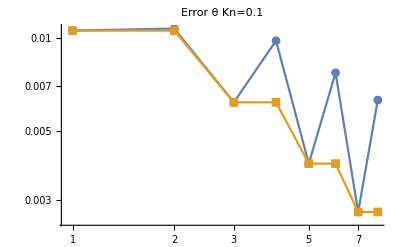

```mathematica
ListLogLogPlot[{errorθKn0p1Grad,errorθKn0p1TrunGrad},Joined->True,PlotLabel->"Error θ Kn=0.1",PlotMarkers->Automatic]
```

```mathematica
errorσKn0p1Grad = Table[ComputeL2Diff[(√2)/3(2solHCGradKn0p1[ii][x]⟦4⟧-solHCGradKn0p1[ii][x]⟦6⟧-solHCGradKn0p1[ii][x]⟦7⟧),σExactHCKn0p1[x]],{ii,3,10}];

errorσKn0p1TrunGrad = Table[ComputeL2Diff[(√2)/3(2solHCTrunGradKn0p1[ii][x]⟦4⟧-solHCTrunGradKn0p1[ii][x]⟦6⟧-solHCTrunGradKn0p1[ii][x]⟦7⟧),σExactHCKn0p1[x]],{ii,3,10}];
```

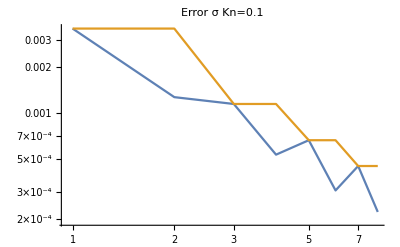

```mathematica
ListLogLogPlot[{errorσKn0p1Grad,errorσKn0p1TrunGrad},Joined->True,PlotLabel->"Error σ Kn=0.1"]
```

#### Error Entropy

```mathematica
errorEntropyTrunGradKn0p1=Quiet[Table[ComputeEntropyDiff[solHCTrunGradKn0p1[15][x],solHCTrunGradKn0p1[ii][x],varTrun[15],varTrun[ii]],{ii,3,10}]];
```

```mathematica
errorEntropyGradKn0p1=Quiet[Table[ComputeEntropyDiff[solHCTrunGradKn0p1[15][x],solHCGradKn0p1[ii][x],varTrun[15],varGrad[ii]],{ii,3,10}]];
```

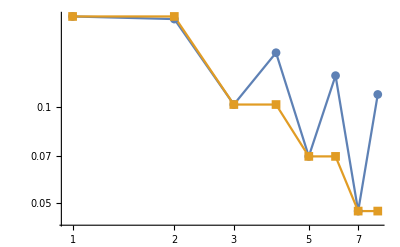

```mathematica
ListLogLogPlot[{errorEntropyGradKn0p1,errorEntropyTrunGradKn0p1},Joined->True,PlotMarkers->Automatic]
```

# Poisson Shear

```mathematica
Clear[solHCGradKn0p1]
```

### Kn = 0.1

```mathematica
vW = 1;
Kn = 0.1;
alpha = 1;
problemType = 0;
```

```mathematica
(*GetSolutionHeat[M_,θW_,kn_,alpha_,flag_,problemtype_]*)

systemType = 0;
Do[Print[Style["Ntensors: ",FontColor->Pink]];Print[ii];
solPoissonShearGradKn0p1[ii][x]=GetSolutionMomentum[ii,vW,Kn,alpha,systemType,problemType];
varGrad[ii]=variables;,{ii,3,10}];
```

Ntensors:

3

0

Poisson Shear

Ntensors:

4

0

Poisson Shear

Ntensors:

5

0

Poisson Shear

Ntensors:

6

0

Poisson Shear

Ntensors:

7

0

Poisson Shear

Ntensors:

8

0

Poisson Shear

Ntensors:

9

0

Poisson Shear

Ntensors:

10

0

Poisson Shear

```mathematica
systemType = 1;
solPoissonShearTrunGradKn0p1[15][x]=GetSolutionMomentum[15,vW,Kn,alpha,systemType,problemType];
varTrun[15]=variables;
```

0

Poisson Shear

```mathematica
systemType=1;
Do[Print[Style["Ntensors: ",FontColor->Pink]];Print[ii];
solPoissonShearTrunGradKn0p1[ii][x]=GetSolutionMomentum[ii,vW,Kn,alpha,systemType,problemType];
varTrun[ii]=variables;,{ii,3,10}];
```

Ntensors:

3

0

Poisson Shear

Ntensors:

4

0

Poisson Shear

Ntensors:

5

0

Poisson Shear

Ntensors:

6

0

Poisson Shear

Ntensors:

7

0

Poisson Shear

Ntensors:

8

0

Poisson Shear

Ntensors:

9

0

Poisson Shear

Ntensors:

10

0

Poisson Shear

### Error Computation

#### Error Macroscopic

```mathematica
errorvyKn0p1Grad = Table[ComputeL2Diff[solPoissonShearGradKn0p1[ii][x]⟦3⟧,vyExactPoissonShearKn0p1[x]],{ii,4,10}];
errorvyKn0p1TrunGrad = Table[ComputeL2Diff[solPoissonShearTrunGradKn0p1[ii][x]⟦3⟧,vyExactPoissonShearKn0p1[x]],{ii,3,10}];
```

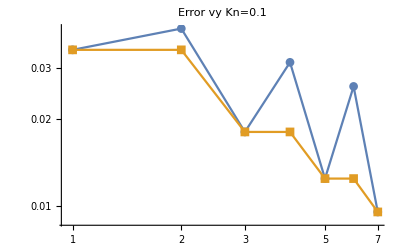

```mathematica
ListLogLogPlot[{errorvyKn0p1Grad,errorvyKn0p1TrunGrad},Joined->True,PlotLabel->"Error vy Kn=0.1",PlotMarkers->Automatic]
```

```mathematica
errorqyKn0p1Grad = Flatten[Table[ComputeL2Diff[Developqy[solPoissonShearGradKn0p1[ii][x],varGrad[ii]],qyExactPoissonShearKn0p1[x]],{ii,4,10}]];

errorqyKn0p1TrunGrad = Flatten[Table[ComputeL2Diff[Developqy[solPoissonShearTrunGradKn0p1[ii][x],varTrun[ii]],qyExactPoissonShearKn0p1[x]],{ii,4,10}]];
```

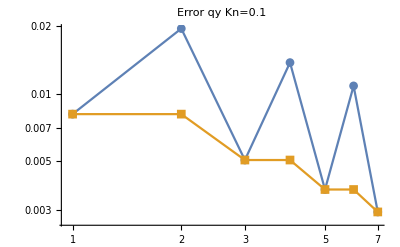

```mathematica
ListLogLogPlot[{errorqyKn0p1Grad,errorqyKn0p1TrunGrad},Joined->True,PlotLabel->"Error qy Kn=0.1",PlotMarkers->Automatic]
```

#### Error Entropy

```mathematica
errorEntropyTrunGradKn0p1=Table[ComputeEntropyDiff[solPoissonShearTrunGradKn0p1[15][x],solPoissonShearTrunGradKn0p1[ii][x],varTrun[15],varTrun[ii]],{ii,3,10}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
errorEntropyGradKn0p1=Table[ComputeEntropyDiff[solPoissonShearTrunGradKn0p1[15][x],solPoissonShearGradKn0p1[ii][x],varTrun[15],varGrad[ii]],{ii,3,10}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

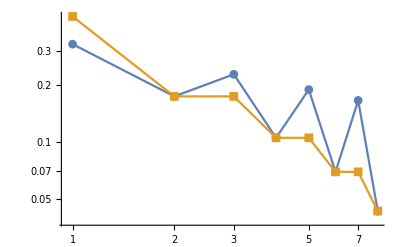

```mathematica
ListLogLogPlot[{errorEntropyGradKn0p1,errorEntropyTrunGradKn0p1},Joined->True,PlotMarkers->Automatic]
```

# Shear

```mathematica
Clear[solHCGradKn0p1]
```

### Kn = 0.1

```mathematica
vW = 1;
Kn = 0.1;
alpha = 0;
problemType = 1;
```

```mathematica
systemType = 0;
Do[Print[Style["Ntensors: ",FontColor->Pink]];Print[ii];
solShearGradKn0p1[ii][x]=GetSolutionMomentum[ii,vW,Kn,alpha,systemType,problemType];
varGrad[ii]=variables;,{ii,3,10}];
```

Ntensors:

3

1

Shear

Ntensors:

4

1

Shear

Ntensors:

5

1

Shear

Ntensors:

6

1

Shear

Ntensors:

7

1

Shear

Ntensors:

8

1

Shear

Ntensors:

9

1

Shear

Ntensors:

10

1

Shear

```mathematica
systemType=1;
solShearTrunGradKn0p1[15][x]=GetSolutionMomentum[15,vW,Kn,alpha,systemType,problemType];
varTrun[15]=variables;
```

1

Shear

```mathematica
systemType=1;
Do[Print[Style["Ntensors: ",FontColor->Pink]];Print[ii];
solShearTrunGradKn0p1[ii][x]=GetSolutionMomentum[ii,vW,Kn,alpha,systemType,problemType];
varTrun[ii]=variables;,{ii,3,10}];
```

Ntensors:

3

1

Shear

Ntensors:

4

1

Shear

Ntensors:

5

1

Shear

Ntensors:

6

1

Shear

Ntensors:

7

1

Shear

Ntensors:

8

1

Shear

Ntensors:

9

1

Shear

Ntensors:

10

1

Shear

### Error Computation

#### Error Macroscopic

```mathematica
errorvyKn0p1Grad = Table[ComputeL2Diff[solShearGradKn0p1[ii][x]⟦3⟧,vyExactShearKn0p1[x]],{ii,3,10}];
errorvyKn0p1TrunGrad = Table[ComputeL2Diff[solShearTrunGradKn0p1[ii][x]⟦3⟧,vyExactShearKn0p1[x]],{ii,3,10}];
```

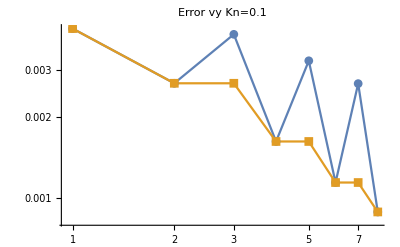

```mathematica
ListLogLogPlot[{errorvyKn0p1Grad,errorvyKn0p1TrunGrad},Joined->True,PlotLabel->"Error vy Kn=0.1",PlotMarkers->Automatic]
```

```mathematica
errorqyKn0p1Grad = Flatten[Table[ComputeL2Diff[Developqy[solShearGradKn0p1[ii][x],varGrad[ii]],qyExactShearKn0p1[x]],{ii,4,10}]];

errorqyKn0p1TrunGrad = Flatten[Table[ComputeL2Diff[Developqy[solShearTrunGradKn0p1[ii][x],varTrun[ii]],qyExactShearKn0p1[x]],{ii,4,10}]];
```

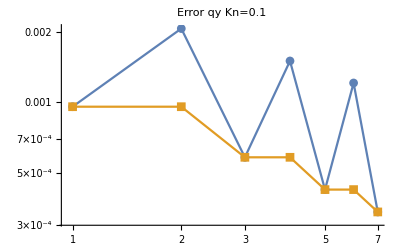

```mathematica
ListLogLogPlot[{errorqyKn0p1Grad,errorqyKn0p1TrunGrad},Joined->True,PlotLabel->"Error qy Kn=0.1",PlotMarkers->Automatic]
```

#### Error Entropy

```mathematica
errorEntropyTrunGradKn0p1=Table[ComputeEntropyDiff[solShearTrunGradKn0p1[15][x],solShearTrunGradKn0p1[ii][x],varTrun[15],varTrun[ii]],{ii,3,10}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
errorEntropyGradKn0p1=Table[ComputeEntropyDiff[solShearTrunGradKn0p1[15][x],solShearGradKn0p1[ii][x],varTrun[15],varGrad[ii]],{ii,3,10}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

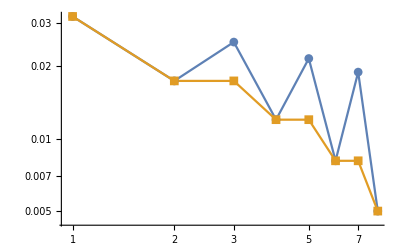

```mathematica
ListLogLogPlot[{errorEntropyGradKn0p1,errorEntropyTrunGradKn0p1},Joined->True,PlotMarkers->Automatic]
```